```mathematica
cosgamma[lam0_,the0_,lam1_,the1_]:=Cos[the0]Cos[the1]Cos[lam1-lam0]+Sin[the0]Sin[the1];
```

## Gaussian vortex (sphere)

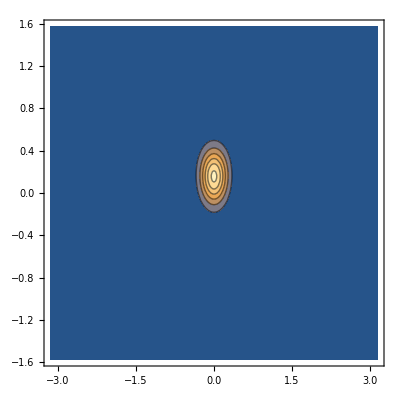

```mathematica
gvsphere[lam_,the_]:=4Pi Exp[-16ArcCos[cosgamma[lam,the,0,Pi/20]]^2];
ContourPlot[gvsphere[lam,the],{lam,-Pi,Pi},{the,-Pi/2,Pi/2},PlotRange->All]
```